## GetCellzillaModel Example File

LGPL license applies. 
See http://xlr8r.info; http: cellzilla.info for additional information.

```mathematica
<<Cellzilla2D.m
```

```mathematica
<<xlr8r.m
```

```mathematica
<<CelleratorML.m
```

Read in the Cellzilla Model from the file "rings.xml"; this file also refers to the Cellerator model in "ring.xml".

```mathematica
czm=GetCellzillaModel["rings.xml"]
```

File: rings.xml

CellzillaML version: 1.0

Creation Date: 2009-06-20T11:55:11

Mathematica: Version 7. release 1 on Linux x86 (64-bit)

Model Name: CellzillaModel

⟶ Importing CelleratorML file: ring.xml

Model: Model4

CelleratorML Version: 1.0

3 reactions

2 parameters

3 initial values

Circuits: {{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}}

local parameters (may be superceded): {v→1,K→0.5}

frozenVariables from models: {}

Global parameters: {DX→9,DY→10,DZ→11}

Joined parameters: {DX→9,DY→10,DZ→11,K→0.5,v→1}

ic: {X→{1.19902,1.88948,2.91279,0.733619,2.35648,2.44333,1.35115,0.702312,0.42276,1.96925},XP→{0,0,0,0,0,0,0,0,0,0},Y→{2.52429,2.75598,0.380217,1.99829,2.83787,0.882576,1.07967,1.67551,0.786751,0.550817},YP→{0,0,0,0,0,0,0,0,0,0},Z→{2.86029,0.79807,2.95751,1.48749,2.72524,2.52888,1.17391,2.48374,2.68445,2.87144},ZP→{0,0,0,0,0,0,0,0,0,0}}

Diffusing Species: {{X,DX},{Y,DY},{Z,DZ}}

{Circuit→{{(X⟺XP)_ZP^Z,MM[K,v,K,v]},{(Y⟺YP)_XP^X,MM[K,v,K,v]},{(Z⟺ZP)_YP^Y,MM[K,v,K,v]}},Parameters→{DX→9,DY→10,DZ→11,K→0.5,v→1},IC→{X→{1.19902,1.88948,2.91279,0.733619,2.35648,2.44333,1.35115,0.702312,0.42276,1.96925},XP→{0,0,0,0,0,0,0,0,0,0},Y→{2.52429,2.75598,0.380217,1.99829,2.83787,0.882576,1.07967,1.67551,0.786751,0.550817},YP→{0,0,0,0,0,0,0,0,0,0},Z→{2.86029,0.79807,2.95751,1.48749,2.72524,2.52888,1.17391,2.48374,2.68445,2.87144},ZP→{0,0,0,0,0,0,0,0,0,0}},DiffusingSpecies→{{X,DX},{Y,DY},{Z,DZ}},Tissue→Tissue[{{-0.643184,6.94854},{-0.629531,8.07477},{-0.192618,8.6986},{-0.0184416,4.75551},{0.140861,5.81942},{0.186136,10.0399},{0.606048,3.48967},{0.695768,10.4575},{1.57374,6.22337},{2.08195,2.54529},{2.10748,2.0316},{2.68839,7.81048},{3.1343,0.324317},{3.56905,10.0298},{3.83631,8.5089},{3.98967,-0.121626},{4.22169,9.34871},{4.4963,4.34976},{4.78704,4.42888},{5.68211,9.51867},{5.81529,0.305081},{5.93909,4.15035},{6.44709,10.5261},{6.52055,-0.168814},{6.57437,8.53016},{6.63053,4.41042},{7.90901,4.35519},{8.13005,-0.101681},{8.40212,0.106901},{8.9168,4.603},{9.28295,11.0049},{9.39151,7.89679},{9.62372,4.19713},{9.73586,10.6322},{9.739,7.37022},{10.2688,0.581981},{10.6457,1.04687}},{{1,2},{1,5},{2,3},{3,6},{3,12},{4,5},{4,7},{5,9},{6,8},{7,10},{8,14},{9,12},{9,18},{10,11},{10,18},{11,13},{12,15},{13,16},{14,17},{15,17},{15,19},{16,21},{17,20},{18,19},{19,22},{20,23},{20,25},{21,22},{21,24},{22,26},{23,31},{24,28},{25,26},{25,32},{26,27},{27,29},{27,30},{28,29},{29,36},{30,33},{30,35},{31,34},{32,34},{32,35},{33,37},{36,37}},{{15,14,16,18,22,28,25,24},{35,37,41,44,34,33},{4,5,17,20,19,11,9},{12,13,24,21,17},{36,39,46,45,40,37},{26,27,34,43,42,31},{28,29,32,38,36,35,30},{20,21,25,30,33,27,23},{6,7,10,15,13,8},{1,2,8,12,5,3}}]}

Run a simulation on this data

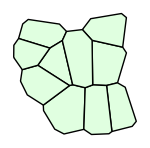

```mathematica
ShowTissue["Tissue"/.czm, ImageSize-> 150]
```

```mathematica
bignet=CelleratorNetwork["Circuit"/.czm, "DiffusingSpecies"/.czm, 
"Tissue"/.czm, "Quiet"-> True];
```

```mathematica
sim=RunSim[bignet,"Parameters"/.czm, ListICToCellzillaIC["IC"/.czm],
{0,15}];
```

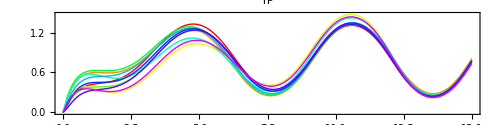

```mathematica
SimPlot[sim,YP, "ImageSize"-> 500, "AspectRatio"-> .25]
```